```mathematica
(*test of nMeas w/ ne=4, 0.05*0.05 loop, steplength = 0.01.*)
```

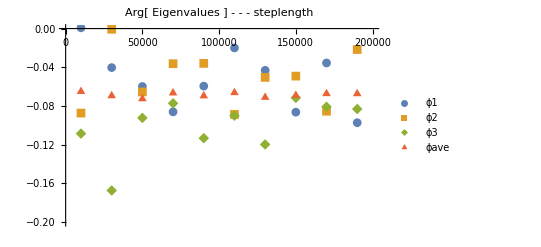

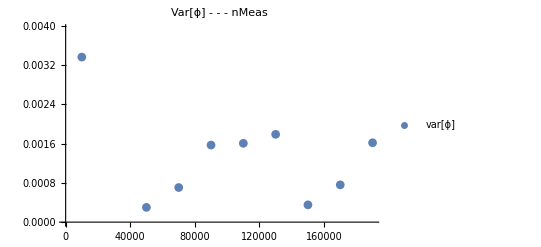

```mathematica
bm=Import["Google Drive/jie_programs/QHlattice/test_error/test_error_nMeas_slne4","Table"];
n:=Length[bm]
x=Table[bm[[i]][[1]],{i,1,n}];
phase1= Table[{x[[i]],bm[[i]][[2]]},{i,1,n}];
phase2= Table[{x[[i]],bm[[i]][[3]]},{i,1,n}];
phase3= Table[{x[[i]],bm[[i]][[4]]},{i,1,n}];
ave=Table[(bm[[i]][[2]]+bm[[i]][[3]]+bm[[i]][[4]])/3,{i,n}];
phaseave= Table[{x[[i]],ave[[i]]},{i,1,n}];
ϕ1dif= Table[{x[[i]],bm[[i]][[2]]-ave[[i]]},{i,1,n}];
ϕ2dif= Table[{x[[i]],bm[[i]][[3]]-ave[[i]]},{i,1,n}];
ϕ3dif= Table[{x[[i]],bm[[i]][[4]]-ave[[i]]},{i,1,n}];


ListPlot[{phase1,phase2,phase3,phaseave},PlotLegends->{"ϕ1","ϕ2", "ϕ3","ϕave"},PlotMarkers->Automatic, PlotLabel->"Arg[ Eigenvalues ] - - - steplength",PlotRange->{{0,200000},{-0.2,0.0}}]

phase=Table[Table[bm[[k]][[i]],{k,n}],{i,2,4}];
varphase=Table[{x[[i]],Variance[phase][[i]]},{i,n}];
varphase2=Table[{x[[i]],Variance[phase][[i]]/(ave[[i]])^2},{i,n}];
ListPlot[varphase,PlotLegends->{"var[ϕ]"},PlotMarkers->Automatic, PlotLabel->"Var[ϕ] - - - nMeas"]
```